{{Denileukin diftitox,Aldesleukin,1},{Darbepoetin alfa,Erythropoietin,1},{Salmon calcitonin,Pramlintide,1},{Asparaginase Escherichia coli,Pegaspargase,1},{Desmopressin,Terlipressin,1},{Imiglucerase,Alglucerase,1},{Abciximab,Tirofiban,1},{Alpha-1-proteinase inhibitor,Filgrastim,1},14670,{Butriptyline,Vortioxetine,1},{Butriptyline,Brexpiprazole,1},{Butriptyline,Dosulepin,1},{Butriptyline,Zotepine,1},{Butriptyline,Acrivastine,1},{Butriptyline,Thonzylamine,1},{Butriptyline,Bilastine,1},{Butriptyline,Rupatadine,1}}
 |  |  |  |

{Denileukin diftitox→Aldesleukin,Darbepoetin alfa→Erythropoietin,Salmon calcitonin→Pramlintide,Asparaginase Escherichia coli→Pegaspargase,Desmopressin→Terlipressin,Imiglucerase→Alglucerase,Abciximab→Tirofiban,Alpha-1-proteinase inhibitor→Filgrastim,Pentagastrin→Cholecystokinin,14668,Dexmethylphenidate→Zotepine,Butriptyline→Vortioxetine,Butriptyline→Brexpiprazole,Butriptyline→Dosulepin,Butriptyline→Zotepine,Butriptyline→Acrivastine,Butriptyline→Thonzylamine,Butriptyline→Bilastine,Butriptyline→Rupatadine}
 |  |  |  |

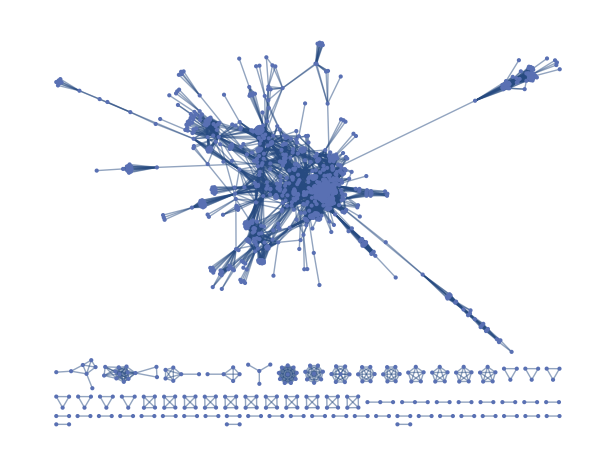

```mathematica
data=Import["C:\\DrugBank\\5.1.7\\Mathematica\\edges517.csv"]
edges= Map[If[#[[3]]>0.0,#[[1]]->#[[2]],Nothing]&,data]
gf=UndirectedGraph[edges]
```

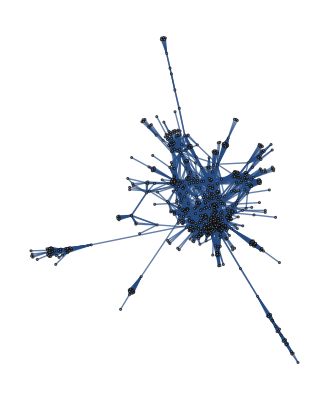

```mathematica
lcgf = Subgraph[gf, First[ConnectedComponents[gf]]]
```

```mathematica
CommunityGraphPlot[lcgf,Method->{"Modularity","Weighted"->True}, CommunityBoundaryStyle->Automatic, CommunityLabels->{"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19", "20",  "21", "22", "23", "24", "25", "26", "27", "28", "29", "30", "31", "32", "33", "34", "35", "36", "37", "38", "39"}]
```

-Graphics-

```mathematica
comunities =FindGraphCommunities[lcgf, Method->{"Modularity","Weighted"->True}]
```

{{Idelalisib,Fostamatinib,Copanlisib,Abemaciclib,Vemurafenib,Regorafenib,Dabrafenib,Encorafenib,Palbociclib,Ribociclib,Trametinib,Binimetinib,Valbenazine,Baricitinib,Sorafenib,Imatinib,Dasatinib,Sunitinib,Nilotinib,Ramucirumab,Pazopanib,Midostaurin,Axitinib,Cabozantinib,Ponatinib,Lenvatinib,Nintedanib,Olaratumab,Bosutinib,Sirolimus,Everolimus,Temsirolimus,Ibrutinib,Crizotinib,Ceritinib,Alectinib,Diacerein,Auranofin,Acetylcysteine,Ruxolitinib,Tofacitinib,Prenylamine,Cetuximab,Gefitinib,Erlotinib,Lapatinib,Vandetanib,Afatinib,Osimertinib,Necitumumab,Neratinib,Dacomitinib,Thalidomide,Diethylcarbamazine,Sulfasalazine,Meclofenamic acid,Balsalazide,Masoprocol,Aminosalicylic acid,Montelukast,Troglitazone,Thiopental,Brigatinib,Lorlatinib,Arsenic trioxide,Cobimetinib,Pentosan polysulfate,Amlexanox,Sucralfate,Triflusal,Ritonavir,Pentobarbital,Bezafibrate,Prasterone,Fenofibric acid,Troleandomycin,Rilpivirine,Mephenytoin,Carbamazepine,Ethotoin,Methylphenobarbital,Ethinylestradiol,Fenofibrate,Rifampicin,Clonazepam,Nifedipine,Sulfinpyrazone,Phenobarbital,Rifaximin,Infliximab,Chloroquine,Tenoxicam,Tolmetin,Rofecoxib,Piroxicam,Fenoprofen,Valdecoxib,Sulindac,Etodolac,Mefenamic acid,Phenylbutazone,Diflunisal,Suprofen,Bromfenac,Oxaprozin,Lenalidomide,Indomethacin,Lumiracoxib,Salsalate,Tiaprofenic acid,Etoricoxib,Nimesulide,Lornoxicam,Aceclofenac,Nepafenac,Parecoxib,Pomalidomide,Dexibuprofen,Dexketoprofen,Tolfenamic acid,Phenyl salicylate,Alclofenac,Acemetacin,Clenbuterol,Amrinone,Rosiglitazone,Nateglinide,Flufenamic acid,Telmisartan,Glipizide,Amiodarone,Pioglitazone,Repaglinide,Zafirlukast,Methadone,Secobarbital,Butabarbital,Butalbital,Talbutal,Amobarbital,Butobarbital,Fluciclovine (18F),Isoflurane,Primidone,Indinavir,Darunavir,Fosamprenavir,Lopinavir,Amprenavir,Tipranavir,Atazanavir,Saquinavir,Esketamine,Guaifenesin,Gemfibrozil,Treprostinil,Acitretin,Clofibrate,Topiramate,Rifabutin,Lesinurad,Hydroxychloroquine,Dinoprostone,Iloprost,Dinoprost,Chlorpropamide,Tolbutamide,Gliquidone,Losartan,Eprosartan,Valsartan,Olmesartan,Irbesartan,Azilsartan medoxomil,Bethanidine,Desflurane,Sevoflurane,Methoxyflurane,Perampanel,Varenicline,Enflurane,Acamprosate,Etomidate,Meprobamate,Carisoprodol,Zolpidem,Halothane,Calcium citrate,Calcium levulinate,Glutethimide,Methyprylon,Thiamylal,Glimepiride,Felbamate,Ifenprodil,Probenecid,Avatrombopag,Epoprostenol,Selexipag,Carboprost tromethamine,Misoprostol,Gemeprost,Acetohexamide,Glymidine,Phenformin,Vinblastine,Levamisole,Rufinamide,Eszopiclone,Cinacalcet,Etelcalcetide,Romiplostim,Eltrombopag,Lusutrombopag},{Pseudoephedrine,Azelastine,Lamotrigine,Olopatadine,Dronedarone,Verapamil,Nicardipine,Cinnarizine,Propiverine,Milnacipran,Meclizine,Quinidine,Imipramine,Chlorpromazine,Pimozide,Trifluoperazine,Phenoxybenzamine,Fluphenazine,Perphenazine,Flunarizine,Minaprine,Amoxapine,Fluvoxamine,Phentermine,Citalopram,Benzatropine,Venlafaxine,Protriptyline,Fluoxetine,Nortriptyline,Fenfluramine,Mazindol,Trazodone,Paroxetine,Trimipramine,Reboxetine,Atomoxetine,Methylphenidate,Meperidine,Modafinil,Epinastine,Lisuride,Apomorphine,Ergotamine,Pramipexole,Dihydroergotamine,Mianserin,Butriptyline,Dosulepin,Zotepine,Vortioxetine,Orphenadrine,Dopamine,Sertraline,Sibutramine,Nefazodone,Desipramine,Escitalopram,Dexfenfluramine,Clomipramine,Tapentadol,Vilazodone,Desvenlafaxine,Dexmethylphenidate,Maprotiline,Diethylpropion,Bupropion,Chloroprocaine,Armodafinil,Viloxazine,Lofexidine,Bromocriptine,Pergolide,Pindolol,Sulpiride,Olanzapine,Doxazosin,Dihydroergocristine,Ziprasidone,Buclizine,Clozapine,Promazine,Cyproheptadine,Brompheniramine,Clemastine,Cetirizine,Terfenadine,Doxylamine,Mirtazapine,Dexbrompheniramine,Triprolidine,Prochlorperazine,Astemizole,Azatadine,Risperidone,Carbinoxamine,Propiomazine,Methdilazine,Ketotifen,Fexofenadine,Desloratadine,Zuclopenthixol,Iloperidone,Pizotifen,Asenapine,Cariprazine,Phenindamine,Clofedanol,Mepyramine,Alcaftadine,Antazoline,Dimetindene,Chlorcyclizine,Acrivastine,Thonzylamine,Bilastine,Rupatadine,Quetiapine,Chlorprothixene,Methotrimeprazine,Emedastine,Levocabastine,Cyclizine,Aripiprazole,Alimemazine,Paliperidone,Halofantrine,Alfuzosin,Prazosin,Loxapine,Remoxipride,Droperidol,Haloperidol,Methysergide,Cabergoline,Dapiprazole,Ropinirole,Periciazine,Pipotiazine,Thiothixene,Silodosin,Brexpiprazole,Fluspirilene,Flibanserin,Sertindole,Amisulpride,Lurasidone,Indoramin,Quinagolide,Flupentixol,Molindone,Ondansetron,Memantine,Yohimbine,Penbutolol,Rotigotine,Propranolol,Carvedilol,Thioridazine,Terazosin,Phentolamine,Nicergoline,Tamsulosin,Tolazoline,Fenoldopam,Mesoridazine,Tegaserod,Levodopa,Betahistine,Pitolisant,Dextroamphetamine,Hydroxyzine,Cisapride,Dofetilide,Ibutilide,Triflupromazine,Thiethylperazine,Buspirone,Tetrabenazine,Metoclopramide,Domperidone,Acetophenazine,Eletriptan,Zolmitriptan,Agomelatine,Naratriptan,Methylergometrine,Alverine,Cevimeline,Succinylcholine,Carbamoylcholine,Methohexital,Metixene,Flumazenil,Pipradrol,Pimavanserin,Almotriptan,Rizatriptan,Frovatriptan,Moxisylyte,Gadopentetic acid,Dacarbazine,Lercanidipine,Prucalopride,Betazole,Pheniramine,Bethanechol},{Leflunomide,Drotaverine,Thimerosal,Diethylstilbestrol,Flutamide,Mexiletine,Nimodipine,Atovaquone,Teriflunomide,Nilvadipine,Amlodipine,Isradipine,Nisoldipine,Felodipine,Nitrendipine,Isavuconazole,Danazol,Raloxifene,Medroxyprogesterone acetate,Norgestimate,Estramustine,Pentazocine,Fluoxymesterone,Oxandrolone,Oxymetholone,Methyltestosterone,Norelgestromin,Stanozolol,Norgestrel,Apalutamide,Estriol,Lasofoxifene,Pentoxyverine,Disopyramide,Phenytoin,Moricizine,Riluzole,Benzonatate,Zonisamide,Procainamide,Tocainide,Propafenone,Flecainide,Encainide,Fosphenytoin,Ajmaline,Desogestrel,Levonorgestrel,Estrone,Dienestrol,Phenolphthalein,Polyestradiol phosphate,Loperamide,Pinaverium,Dalfampridine,Bendroflumethiazide,Benzthiazide,Trichlormethiazide,Quinethazone,Diazoxide,Diclofenamide,Brinzolamide,Cyclothiazide,Methazolamide,Hydroflumethiazide,Acetazolamide,Dorzolamide,Chlorothiazide,Crofelemer,Bumetanide,Glyburide,Nylidrin,Gestrinone,Drospirenone,Cyproterone acetate,Enzalutamide,Dienogest,Mitotane,Nilutamide,Bicalutamide,Fluticasone,Fluticasone furoate,Eplerenone,Sotalol,Dextropropoxyphene,Naltrexone,Buprenorphine,Naloxone,Dezocine,Alvimopan,Pholcodine,Naldemedine,Codeine,Hydromorphone,Morphine,Trimebutine,Oxycodone,Butorphanol,Sufentanil,Alfentanil,Fentanyl,Remifentanil,Anileridine,Diphenoxylate,Levacetylmethadol,Diamorphine,Eluxadoline,Opium,Bepridil,Amsacrine,Cyclandelate,Trimethadione,Ethosuximide,Methsuximide,Levetiracetam,Ziconotide,Chlorthalidone,Methocarbamol,Etonogestrel,Megestrol acetate,Dydrogesterone,Tocofersolan,Nalbuphine,Nalmefene,Naloxegol,Clomifene,Fulvestrant,Melatonin,Mifepristone,Bazedoxifene,Tibolone,Budesonide,Ulipristal,Ospemifene,Dronabinol,Nabilone,Phenacemide,Phenazopyridine,Nitrazepam,Lacidipine,Metergoline,Clofazimine,Etacrynic acid,Hydrochlorothiazide,Polythiazide,Metolazone,Indapamide,Digoxin,Acetyldigitoxin,Deslanoside,Ouabain,Bretylium,Digitoxin,Torasemide,Piretanide,Perhexiline,Probucol,Peginterferon alfa-2a,Interferon alfa-n1,Peginterferon alfa-2b,Interferon beta-1b,Cetrorelix,Abarelix,Degarelix,Ganirelix,Deflazacort,Prednisone,Fludrocortisone,Rimexolone,Ciclesonide,Difluprednate,Flunisolide,Medrysone,Fluorometholone,Dequalinium,Cefdinir,Tasimelteon,Interferon beta-1a},{Atorvastatin,Procaine,Carteolol,Norepinephrine,Clonidine,Midodrine,Metaraminol,Methoxamine,Phenylpropanolamine,Dexmedetomidine,Orciprenaline,Dobutamine,Celiprolol,Metamfetamine,Xylometazoline,Isometheptene,Moxonidine,Olodaterol,Vilanterol,Indacaterol,Droxidopa,Xamoterol,Terbutaline,Apraclonidine,Ergometrine,Ritodrine,Salmeterol,Formoterol,Salbutamol,Guanfacine,Isoprenaline,Arbutamine,Acebutolol,Fenoterol,Pirbuterol,Procaterol,Nebivolol,Mirabegron,Ranolazine,Tranylcypromine,Phenelzine,Selegiline,Amphetamine,Pargyline,Zimelidine,Safinamide,Moclobemide,Isocarboxazid,Rasagiline,Pravastatin,Lovastatin,Valproic acid,Cerivastatin,Simvastatin,Sitagliptin,Vildagliptin,Alogliptin,Saxagliptin,Linagliptin,Fluvastatin,Rosuvastatin,Vorinostat,Romidepsin,Pitavastatin,Esmolol,Betaxolol,Metoprolol,Atenolol,Timolol,Labetalol,Bisoprolol,Nadolol,Levobunolol,Metipranolol,Practolol,Oxprenolol,Procarbazine,Mepivacaine,Levobupivacaine,Reserpine,Deserpidine,Lisdexamfetamine,Brivaracetam,Oxcarbazepine,Dichlorobenzyl alcohol,Pyridoxal phosphate,Vigabatrin,Hydralazine,Mephentermine,Indigotindisulfonic acid,Lifitegrast,Fingolimod},{Methantheline,Famotidine,Nizatidine,Palonosetron,Tropisetron,Tubocurarine,Rocuronium,Dolasetron,Granisetron,Alosetron,Trospium,Oxyphenonium,Ipratropium,Trihexyphenidyl,Oxyphencyclimine,Procyclidine,Profenamine,Darifenacin,Atropine,Fesoterodine,Hexocyclium,Aclidinium,Umeclidinium,Butylscopolamine,Pyrantel,Homatropine,Diphemanil,Pirenzepine,Homatropine methylbromide,Clidinium,Propantheline,Dicyclomine,Tropicamide,Biperiden,Cyclopentolate,Tolterodine,Flavoxate,Tiotropium,Solifenacin,Mepenzolate,Doxacurium,Mivacurium,Pancuronium,Pipecuronium,Isopropamide,Galantamine,Tacrine,Pyridostigmine,Donepezil,Demecarium,Physostigmine,Rivastigmine,Ambenonium,Neostigmine,Vecuronium,Cisatracurium,Mecamylamine,Hexafluronium,Echothiophate},{Cefazolin,Ceftazidime,Mezlocillin,Cefmenoxime,Cefmetazole,Ertapenem,Cefpiramide,Cefoxitin,Imipenem,Latamoxef,Cefonicid,Cefoperazone,Cefepime,Ceftibuten,Doripenem,Ceftizoxime,Cefradine,Cefpodoxime,Piperacillin,Ampicillin,Loracarbef,Cefalotin,Dicloxacillin,Cefotaxime,Cephalexin,Nafcillin,Oxacillin,Hetacillin,Cefaclor,Cyclacillin,Cefadroxil,Cefotetan,Meticillin,Flucloxacillin,Cefditoren,Cloxacillin,Azlocillin,Cefuroxime,Cefapirin,Pivampicillin,Pivmecillinam,Ticarcillin,Meropenem,Cefixime,Ceftriaxone,Aztreonam,Carbenicillin,Bacampicillin,Carindacillin,Phenoxymethylpenicillin,Cefprozil},{Decitabine,Azacitidine,Altretamine,Clofarabine,Oxamniquine,Ifosfamide,Cladribine,Carmustine,Trifluridine,Niclosamide,Plicamycin,Gemcitabine,Hydroxyurea,Fludarabine,Nelarabine,Raltitrexed,Pralatrexate,Tegafur,Methotrexate,Pemetrexed,Capecitabine,Proguanil,Trimetrexate,Pyrimethamine,Sulfadoxine},{Moxifloxacin,Idarubicin,Mitoxantrone,Sparfloxacin,Enoxacin,Pefloxacin,Trovafloxacin,Lomefloxacin,Norfloxacin,Ofloxacin,Daunorubicin,Etoposide,Doxorubicin,Dexrazoxane,Valrubicin,Teniposide,Epirubicin,Besifloxacin,Grepafloxacin,Cinoxacin,Gemifloxacin,Gatifloxacin},{Tadalafil,Vardenafil,Dipyridamole,Avanafil,Udenafil,Theophylline,Aminophylline,Sildenafil,Dyphylline,Pentostatin,Oxtriphylline,Papaverine,Roflumilast,Milrinone,Anagrelide,Mefloquine,Levosimendan,Cilostazol,Enoximone,Quinine,Primaquine},{Stavudine,Delavirdine,Lamivudine,Emtricitabine,Didanosine,Zalcitabine,Abacavir,Nevirapine,Tenofovir disoproxil,Zidovudine,Efavirenz,Tenofovir alafenamide,Bictegravir,Doravirine,Raltegravir,Dolutegravir,Elvitegravir},{Perindopril,Enalapril,Moexipril,Lisinopril,Ramipril,Fosinopril,Trandolapril,Benazepril,Spirapril,Zofenopril,Quinapril,Rescinnamine,Captopril,Cilazapril,Aliskiren},{Gliclazide,Dalteparin,Heparin,Nadroparin,Andexanet alfa,Fondaparinux,Enoxaparin,Rivaroxaban,Apixaban,Edoxaban,Bemiparin},{Conestat alfa,Human C1-esterase inhibitor,Zinc sulfate, unspecified form,Dabigatran etexilate,Lepirudin,Bivalirudin,Argatroban,Ximelagatran,Ecallantide,Lanadelumab,Sulodexide},{Telaprevir,Paritaprevir,Grazoprevir,Voxilaprevir,Boceprevir}}

```mathematica
c1 = First[comunities]
```

{Idelalisib,Fostamatinib,Copanlisib,Abemaciclib,Vemurafenib,Regorafenib,Dabrafenib,Encorafenib,Palbociclib,Ribociclib,Trametinib,Binimetinib,Valbenazine,Baricitinib,Sorafenib,Imatinib,Dasatinib,Sunitinib,Nilotinib,Ramucirumab,Pazopanib,Midostaurin,Axitinib,Cabozantinib,Ponatinib,Lenvatinib,Nintedanib,Olaratumab,Bosutinib,Sirolimus,Everolimus,Temsirolimus,Ibrutinib,Crizotinib,Ceritinib,Alectinib,Diacerein,Auranofin,Acetylcysteine,Ruxolitinib,Tofacitinib,Prenylamine,Cetuximab,Gefitinib,Erlotinib,Lapatinib,Vandetanib,Afatinib,Osimertinib,Necitumumab,Neratinib,Dacomitinib,Thalidomide,Diethylcarbamazine,Sulfasalazine,Meclofenamic acid,Balsalazide,Masoprocol,Aminosalicylic acid,Montelukast,Troglitazone,Thiopental,Brigatinib,Lorlatinib,Arsenic trioxide,Cobimetinib,Pentosan polysulfate,Amlexanox,Sucralfate,Triflusal,Ritonavir,Pentobarbital,Bezafibrate,Prasterone,Fenofibric acid,Troleandomycin,Rilpivirine,Mephenytoin,Carbamazepine,Ethotoin,Methylphenobarbital,Ethinylestradiol,Fenofibrate,Rifampicin,Clonazepam,Nifedipine,Sulfinpyrazone,Phenobarbital,Rifaximin,Infliximab,Chloroquine,Tenoxicam,Tolmetin,Rofecoxib,Piroxicam,Fenoprofen,Valdecoxib,Sulindac,Etodolac,Mefenamic acid,Phenylbutazone,Diflunisal,Suprofen,Bromfenac,Oxaprozin,Lenalidomide,Indomethacin,Lumiracoxib,Salsalate,Tiaprofenic acid,Etoricoxib,Nimesulide,Lornoxicam,Aceclofenac,Nepafenac,Parecoxib,Pomalidomide,Dexibuprofen,Dexketoprofen,Tolfenamic acid,Phenyl salicylate,Alclofenac,Acemetacin,Clenbuterol,Amrinone,Rosiglitazone,Nateglinide,Flufenamic acid,Telmisartan,Glipizide,Amiodarone,Pioglitazone,Repaglinide,Zafirlukast,Methadone,Secobarbital,Butabarbital,Butalbital,Talbutal,Amobarbital,Butobarbital,Fluciclovine (18F),Isoflurane,Primidone,Indinavir,Darunavir,Fosamprenavir,Lopinavir,Amprenavir,Tipranavir,Atazanavir,Saquinavir,Esketamine,Guaifenesin,Gemfibrozil,Treprostinil,Acitretin,Clofibrate,Topiramate,Rifabutin,Lesinurad,Hydroxychloroquine,Dinoprostone,Iloprost,Dinoprost,Chlorpropamide,Tolbutamide,Gliquidone,Losartan,Eprosartan,Valsartan,Olmesartan,Irbesartan,Azilsartan medoxomil,Bethanidine,Desflurane,Sevoflurane,Methoxyflurane,Perampanel,Varenicline,Enflurane,Acamprosate,Etomidate,Meprobamate,Carisoprodol,Zolpidem,Halothane,Calcium citrate,Calcium levulinate,Glutethimide,Methyprylon,Thiamylal,Glimepiride,Felbamate,Ifenprodil,Probenecid,Avatrombopag,Epoprostenol,Selexipag,Carboprost tromethamine,Misoprostol,Gemeprost,Acetohexamide,Glymidine,Phenformin,Vinblastine,Levamisole,Rufinamide,Eszopiclone,Cinacalcet,Etelcalcetide,Romiplostim,Eltrombopag,Lusutrombopag}

```mathematica
c2 = Part[comunities, 2]
```

{Pseudoephedrine,Azelastine,Lamotrigine,Olopatadine,Dronedarone,Verapamil,Nicardipine,Cinnarizine,Propiverine,Milnacipran,Meclizine,Quinidine,Imipramine,Chlorpromazine,Pimozide,Trifluoperazine,Phenoxybenzamine,Fluphenazine,Perphenazine,Flunarizine,Minaprine,Amoxapine,Fluvoxamine,Phentermine,Citalopram,Benzatropine,Venlafaxine,Protriptyline,Fluoxetine,Nortriptyline,Fenfluramine,Mazindol,Trazodone,Paroxetine,Trimipramine,Reboxetine,Atomoxetine,Methylphenidate,Meperidine,Modafinil,Epinastine,Lisuride,Apomorphine,Ergotamine,Pramipexole,Dihydroergotamine,Mianserin,Butriptyline,Dosulepin,Zotepine,Vortioxetine,Orphenadrine,Dopamine,Sertraline,Sibutramine,Nefazodone,Desipramine,Escitalopram,Dexfenfluramine,Clomipramine,Tapentadol,Vilazodone,Desvenlafaxine,Dexmethylphenidate,Maprotiline,Diethylpropion,Bupropion,Chloroprocaine,Armodafinil,Viloxazine,Lofexidine,Bromocriptine,Pergolide,Pindolol,Sulpiride,Olanzapine,Doxazosin,Dihydroergocristine,Ziprasidone,Buclizine,Clozapine,Promazine,Cyproheptadine,Brompheniramine,Clemastine,Cetirizine,Terfenadine,Doxylamine,Mirtazapine,Dexbrompheniramine,Triprolidine,Prochlorperazine,Astemizole,Azatadine,Risperidone,Carbinoxamine,Propiomazine,Methdilazine,Ketotifen,Fexofenadine,Desloratadine,Zuclopenthixol,Iloperidone,Pizotifen,Asenapine,Cariprazine,Phenindamine,Clofedanol,Mepyramine,Alcaftadine,Antazoline,Dimetindene,Chlorcyclizine,Acrivastine,Thonzylamine,Bilastine,Rupatadine,Quetiapine,Chlorprothixene,Methotrimeprazine,Emedastine,Levocabastine,Cyclizine,Aripiprazole,Alimemazine,Paliperidone,Halofantrine,Alfuzosin,Prazosin,Loxapine,Remoxipride,Droperidol,Haloperidol,Methysergide,Cabergoline,Dapiprazole,Ropinirole,Periciazine,Pipotiazine,Thiothixene,Silodosin,Brexpiprazole,Fluspirilene,Flibanserin,Sertindole,Amisulpride,Lurasidone,Indoramin,Quinagolide,Flupentixol,Molindone,Ondansetron,Memantine,Yohimbine,Penbutolol,Rotigotine,Propranolol,Carvedilol,Thioridazine,Terazosin,Phentolamine,Nicergoline,Tamsulosin,Tolazoline,Fenoldopam,Mesoridazine,Tegaserod,Levodopa,Betahistine,Pitolisant,Dextroamphetamine,Hydroxyzine,Cisapride,Dofetilide,Ibutilide,Triflupromazine,Thiethylperazine,Buspirone,Tetrabenazine,Metoclopramide,Domperidone,Acetophenazine,Eletriptan,Zolmitriptan,Agomelatine,Naratriptan,Methylergometrine,Alverine,Cevimeline,Succinylcholine,Carbamoylcholine,Methohexital,Metixene,Flumazenil,Pipradrol,Pimavanserin,Almotriptan,Rizatriptan,Frovatriptan,Moxisylyte,Gadopentetic acid,Dacarbazine,Lercanidipine,Prucalopride,Betazole,Pheniramine,Bethanechol}

```mathematica
c2 = Part[comunities, 3]
```

{Leflunomide,Drotaverine,Thimerosal,Diethylstilbestrol,Flutamide,Mexiletine,Nimodipine,Atovaquone,Teriflunomide,Nilvadipine,Amlodipine,Isradipine,Nisoldipine,Felodipine,Nitrendipine,Isavuconazole,Danazol,Raloxifene,Medroxyprogesterone acetate,Norgestimate,Estramustine,Pentazocine,Fluoxymesterone,Oxandrolone,Oxymetholone,Methyltestosterone,Norelgestromin,Stanozolol,Norgestrel,Apalutamide,Estriol,Lasofoxifene,Pentoxyverine,Disopyramide,Phenytoin,Moricizine,Riluzole,Benzonatate,Zonisamide,Procainamide,Tocainide,Propafenone,Flecainide,Encainide,Fosphenytoin,Ajmaline,Desogestrel,Levonorgestrel,Estrone,Dienestrol,Phenolphthalein,Polyestradiol phosphate,Loperamide,Pinaverium,Dalfampridine,Bendroflumethiazide,Benzthiazide,Trichlormethiazide,Quinethazone,Diazoxide,Diclofenamide,Brinzolamide,Cyclothiazide,Methazolamide,Hydroflumethiazide,Acetazolamide,Dorzolamide,Chlorothiazide,Crofelemer,Bumetanide,Glyburide,Nylidrin,Gestrinone,Drospirenone,Cyproterone acetate,Enzalutamide,Dienogest,Mitotane,Nilutamide,Bicalutamide,Fluticasone,Fluticasone furoate,Eplerenone,Sotalol,Dextropropoxyphene,Naltrexone,Buprenorphine,Naloxone,Dezocine,Alvimopan,Pholcodine,Naldemedine,Codeine,Hydromorphone,Morphine,Trimebutine,Oxycodone,Butorphanol,Sufentanil,Alfentanil,Fentanyl,Remifentanil,Anileridine,Diphenoxylate,Levacetylmethadol,Diamorphine,Eluxadoline,Opium,Bepridil,Amsacrine,Cyclandelate,Trimethadione,Ethosuximide,Methsuximide,Levetiracetam,Ziconotide,Chlorthalidone,Methocarbamol,Etonogestrel,Megestrol acetate,Dydrogesterone,Tocofersolan,Nalbuphine,Nalmefene,Naloxegol,Clomifene,Fulvestrant,Melatonin,Mifepristone,Bazedoxifene,Tibolone,Budesonide,Ulipristal,Ospemifene,Dronabinol,Nabilone,Phenacemide,Phenazopyridine,Nitrazepam,Lacidipine,Metergoline,Clofazimine,Etacrynic acid,Hydrochlorothiazide,Polythiazide,Metolazone,Indapamide,Digoxin,Acetyldigitoxin,Deslanoside,Ouabain,Bretylium,Digitoxin,Torasemide,Piretanide,Perhexiline,Probucol,Peginterferon alfa-2a,Interferon alfa-n1,Peginterferon alfa-2b,Interferon beta-1b,Cetrorelix,Abarelix,Degarelix,Ganirelix,Deflazacort,Prednisone,Fludrocortisone,Rimexolone,Ciclesonide,Difluprednate,Flunisolide,Medrysone,Fluorometholone,Dequalinium,Cefdinir,Tasimelteon,Interferon beta-1a}

```mathematica
c2 = Part[comunities, 4]
```

{Atorvastatin,Procaine,Carteolol,Norepinephrine,Clonidine,Midodrine,Metaraminol,Methoxamine,Phenylpropanolamine,Dexmedetomidine,Orciprenaline,Dobutamine,Celiprolol,Metamfetamine,Xylometazoline,Isometheptene,Moxonidine,Olodaterol,Vilanterol,Indacaterol,Droxidopa,Xamoterol,Terbutaline,Apraclonidine,Ergometrine,Ritodrine,Salmeterol,Formoterol,Salbutamol,Guanfacine,Isoprenaline,Arbutamine,Acebutolol,Fenoterol,Pirbuterol,Procaterol,Nebivolol,Mirabegron,Ranolazine,Tranylcypromine,Phenelzine,Selegiline,Amphetamine,Pargyline,Zimelidine,Safinamide,Moclobemide,Isocarboxazid,Rasagiline,Pravastatin,Lovastatin,Valproic acid,Cerivastatin,Simvastatin,Sitagliptin,Vildagliptin,Alogliptin,Saxagliptin,Linagliptin,Fluvastatin,Rosuvastatin,Vorinostat,Romidepsin,Pitavastatin,Esmolol,Betaxolol,Metoprolol,Atenolol,Timolol,Labetalol,Bisoprolol,Nadolol,Levobunolol,Metipranolol,Practolol,Oxprenolol,Procarbazine,Mepivacaine,Levobupivacaine,Reserpine,Deserpidine,Lisdexamfetamine,Brivaracetam,Oxcarbazepine,Dichlorobenzyl alcohol,Pyridoxal phosphate,Vigabatrin,Hydralazine,Mephentermine,Indigotindisulfonic acid,Lifitegrast,Fingolimod}

```mathematica
c2 = Part[comunities, 5]
```

{Methantheline,Famotidine,Nizatidine,Palonosetron,Tropisetron,Tubocurarine,Rocuronium,Dolasetron,Granisetron,Alosetron,Trospium,Oxyphenonium,Ipratropium,Trihexyphenidyl,Oxyphencyclimine,Procyclidine,Profenamine,Darifenacin,Atropine,Fesoterodine,Hexocyclium,Aclidinium,Umeclidinium,Butylscopolamine,Pyrantel,Homatropine,Diphemanil,Pirenzepine,Homatropine methylbromide,Clidinium,Propantheline,Dicyclomine,Tropicamide,Biperiden,Cyclopentolate,Tolterodine,Flavoxate,Tiotropium,Solifenacin,Mepenzolate,Doxacurium,Mivacurium,Pancuronium,Pipecuronium,Isopropamide,Galantamine,Tacrine,Pyridostigmine,Donepezil,Demecarium,Physostigmine,Rivastigmine,Ambenonium,Neostigmine,Vecuronium,Cisatracurium,Mecamylamine,Hexafluronium,Echothiophate}

```mathematica
c6 = Part[comunities, 6]
```

{Cefazolin,Ceftazidime,Mezlocillin,Cefmenoxime,Cefmetazole,Ertapenem,Cefpiramide,Cefoxitin,Imipenem,Latamoxef,Cefonicid,Cefoperazone,Cefepime,Ceftibuten,Doripenem,Ceftizoxime,Cefradine,Cefpodoxime,Piperacillin,Ampicillin,Loracarbef,Cefalotin,Dicloxacillin,Cefotaxime,Cephalexin,Nafcillin,Oxacillin,Hetacillin,Cefaclor,Cyclacillin,Cefadroxil,Cefotetan,Meticillin,Flucloxacillin,Cefditoren,Cloxacillin,Azlocillin,Cefuroxime,Cefapirin,Pivampicillin,Pivmecillinam,Ticarcillin,Meropenem,Cefixime,Ceftriaxone,Aztreonam,Carbenicillin,Bacampicillin,Carindacillin,Phenoxymethylpenicillin,Cefprozil}

```mathematica
c7 = Part[comunities, 7]
```

{Decitabine,Azacitidine,Altretamine,Clofarabine,Oxamniquine,Ifosfamide,Cladribine,Carmustine,Trifluridine,Niclosamide,Plicamycin,Gemcitabine,Hydroxyurea,Fludarabine,Nelarabine,Raltitrexed,Pralatrexate,Tegafur,Methotrexate,Pemetrexed,Capecitabine,Proguanil,Trimetrexate,Pyrimethamine,Sulfadoxine}

```mathematica
c8 = Part[comunities, 8]
```

{Moxifloxacin,Idarubicin,Mitoxantrone,Sparfloxacin,Enoxacin,Pefloxacin,Trovafloxacin,Lomefloxacin,Norfloxacin,Ofloxacin,Daunorubicin,Etoposide,Doxorubicin,Dexrazoxane,Valrubicin,Teniposide,Epirubicin,Besifloxacin,Grepafloxacin,Cinoxacin,Gemifloxacin,Gatifloxacin}

```mathematica
c9 = Part[comunities, 9]
```

{Tadalafil,Vardenafil,Dipyridamole,Avanafil,Udenafil,Theophylline,Aminophylline,Sildenafil,Dyphylline,Pentostatin,Oxtriphylline,Papaverine,Roflumilast,Milrinone,Anagrelide,Mefloquine,Levosimendan,Cilostazol,Enoximone,Quinine,Primaquine}

```mathematica
c10 = Part[comunities, 10]
```

{Stavudine,Delavirdine,Lamivudine,Emtricitabine,Didanosine,Zalcitabine,Abacavir,Nevirapine,Tenofovir disoproxil,Zidovudine,Efavirenz,Tenofovir alafenamide,Bictegravir,Doravirine,Raltegravir,Dolutegravir,Elvitegravir}

```mathematica
c11 = Part[comunities, 11]
```

{Perindopril,Enalapril,Moexipril,Lisinopril,Ramipril,Fosinopril,Trandolapril,Benazepril,Spirapril,Zofenopril,Quinapril,Rescinnamine,Captopril,Cilazapril,Aliskiren}

```mathematica
c12 = Part[comunities, 12]
```

{Gliclazide,Dalteparin,Heparin,Nadroparin,Andexanet alfa,Fondaparinux,Enoxaparin,Rivaroxaban,Apixaban,Edoxaban,Bemiparin}

```mathematica
c13 = Part[comunities, 13]
```

{Conestat alfa,Human C1-esterase inhibitor,Zinc sulfate, unspecified form,Dabigatran etexilate,Lepirudin,Bivalirudin,Argatroban,Ximelagatran,Ecallantide,Lanadelumab,Sulodexide}

```mathematica
c14 = Part[comunities, 14]
```

{Telaprevir,Paritaprevir,Grazoprevir,Voxilaprevir,Boceprevir}